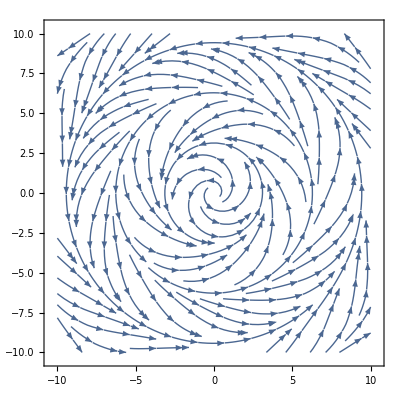

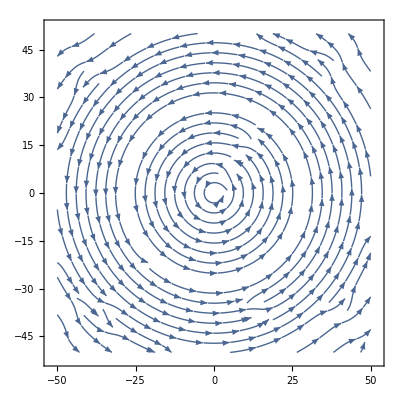

```mathematica
Fx[x_,y_]:= 1/2*x*Sin[Sqrt[x^2+y^2]]-y
Fy[x_,y_]:= 1/2*y*Sin[Sqrt[x^2+y^2]]+x
StreamPlot[{Fx[x,y],Fy[x,y]},{x,-10,10}, {y,-10,10}]
StreamPlot[{Fx[x,y],Fy[x,y]},{x,-50,50}, {y,-50,50}]
```

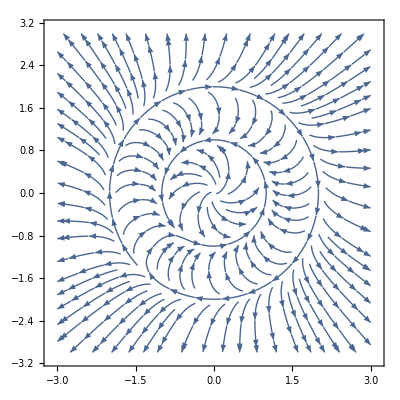

```mathematica
Fx2[x_,y_]:=x(1-x^2-y^2)(4-x^2-y^2)-y(2-x^2-y^2)
Fy2[x_,y_]:=y(1-x^2-y^2)(4-x^2-y^2)+x(2-x^2-y^2)
StreamPlot[{Fx2[x,y],Fy2[x,y]},{x,-3,3}, {y,-3,3}]
```

1

{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

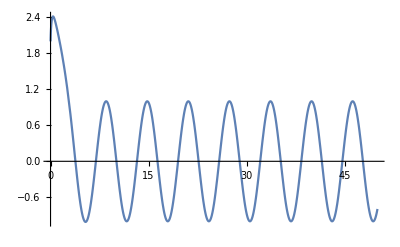

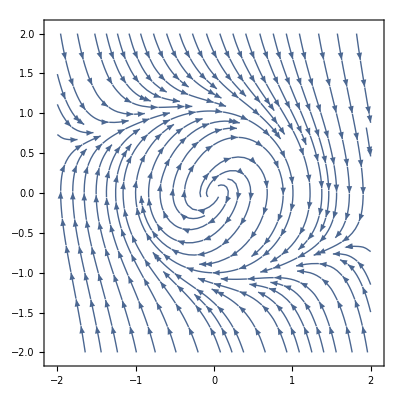

```mathematica
e=1
sol = NDSolve[{x''[t]+e*x'[t]*((x[t])^2+(x'[t])^2-1)+x[t]==0, {x[0]==2,x'[0]==5}},x, {t,0,50}]
Plot[Evaluate[x[t]/.sol], {t,0,50}, PlotRange->All]
Fx3[x_,y_]:=y
Fy3[x_,y_]:=-e*y(x^2+y^2-1)-x
StreamPlot[{Fx3[x,y],Fy3[x,y]},{x,-2,2},{y,-2,2}]
```

0.3

{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

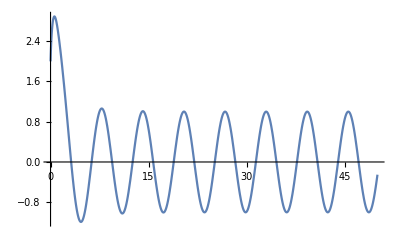

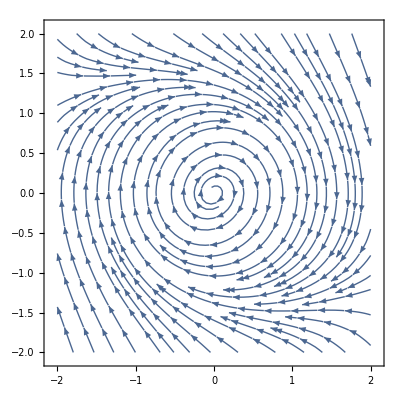

```mathematica
e=0.3
sol = NDSolve[{x''[t]+e*x'[t]*((x[t])^2+(x'[t])^2-1)+x[t]==0, {x[0]==2,x'[0]==5}},x, {t,0,50}]
Plot[Evaluate[x[t]/.sol], {t,0,50}, PlotRange->All]
Fx3[x_,y_]:=y
Fy3[x_,y_]:=-e*y(x^2+y^2-1)-x
StreamPlot[{Fx3[x,y],Fy3[x,y]},{x,-2,2},{y,-2,2}]
```

12

{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

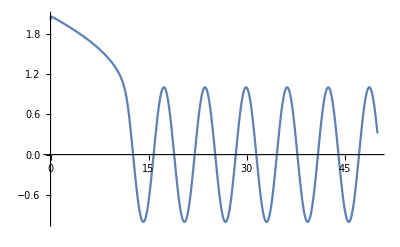

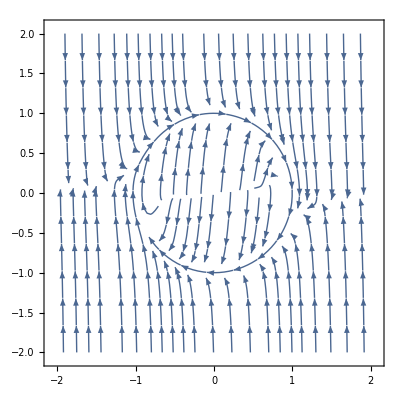

```mathematica
e=12
sol = NDSolve[{x''[t]+e*x'[t]*((x[t])^2+(x'[t])^2-1)+x[t]==0, {x[0]==2,x'[0]==5}},x, {t,0,50}]
Plot[Evaluate[x[t]/.sol], {t,0,50}, PlotRange->All]
Fx3[x_,y_]:=y
Fy3[x_,y_]:=-e*y(x^2+y^2-1)-x
StreamPlot[{Fx3[x,y],Fy3[x,y]},{x,-2,2},{y,-2,2}]
```

1

100

{{x→InterpolatingFunction[{{0., 1000.}}, <>]}}

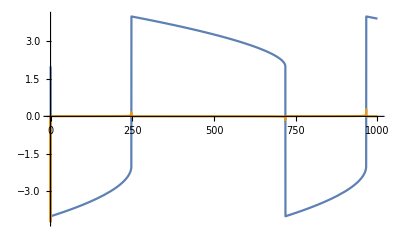

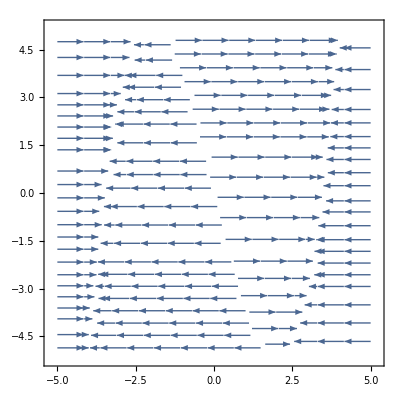

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>]}}

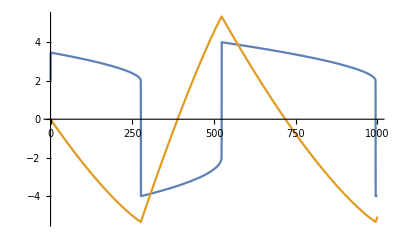

```mathematica
a=1
mi = 100
sol = NDSolve[{x''[t]+mi*x'[t]*((x[t])^2-4)+x[t]==a, {x[0]==2,x'[0]==0}},x, {t,0,1000}]
Plot[Evaluate[{x[t],x'[t]}/.sol], {t,0,1000},PlotRange->All]
Fx4[x_,y_]:=mi(y-(1/3)*x^3+4x)
Fy4[x_,y_]:=(1/mi)(a-x)
StreamPlot[{Fx4[x,y],Fy4[x,y]},{x,-5,5},{y,-5,5}]
sol2=NDSolve[{x'[t]==Fx4[x[t],y[t]],y'[t]==Fy4[x[t],y[t]],{x[0]==2,y[0]==0}},{x,y}, {t,0,1000}]
Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,1000},PlotRange->All]
```

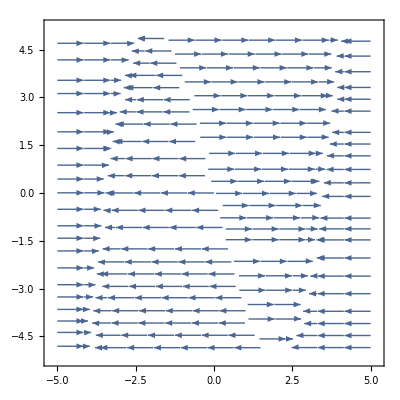

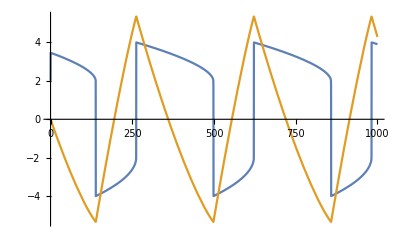

```mathematica
a=1
mi = 50
Fx4[x_,y_]:=mi(y-(1/3)*x^3+4x)
Fy4[x_,y_]:=(1/mi)(a-x)
StreamPlot[{Fx4[x,y],Fy4[x,y]},{x,-5,5},{y,-5,5}]
sol2=NDSolve[{x'[t]==Fx4[x[t],y[t]],y'[t]==Fy4[x[t],y[t]],{x[0]==2,y[0]==0}},{x,y}, {t,0,1000}]
Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,1000},PlotRange->All]
```

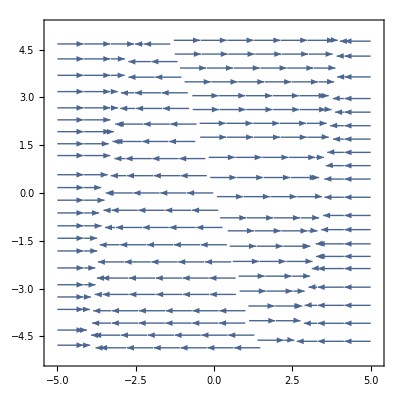

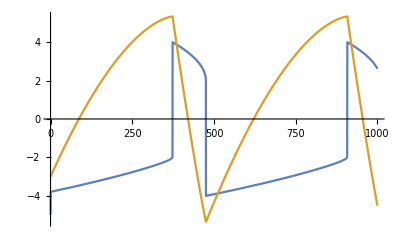

```mathematica
a=-1.9
mi = 50
Fx4[x_,y_]:=mi(y-(1/3)*x^3+4x)
Fy4[x_,y_]:=(1/mi)(a-x)
StreamPlot[{Fx4[x,y],Fy4[x,y]},{x,-5,5},{y,-5,5}]
sol2=NDSolve[{x'[t]==Fx4[x[t],y[t]],y'[t]==Fy4[x[t],y[t]],{x[0]==-5,y[0]==-3}},{x,y}, {t,0,1000}]
Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,1000},PlotRange->All]
```

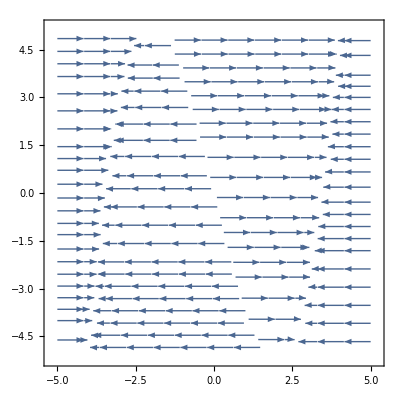

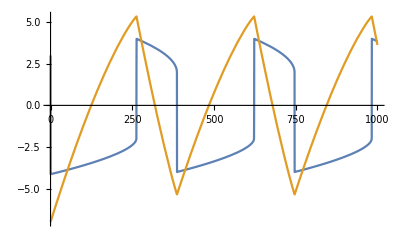

```mathematica
a=-1
mi = 50
Fx4[x_,y_]:=mi(y-(1/3)*x^3+4x)
Fy4[x_,y_]:=(1/mi)(a-x)
StreamPlot[{Fx4[x,y],Fy4[x,y]},{x,-5,5},{y,-5,5}]
sol2=NDSolve[{x'[t]==Fx4[x[t],y[t]],y'[t]==Fy4[x[t],y[t]],{x[0]==3,y[0]==-7}},{x,y}, {t,0,1000}]
Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,1000},PlotRange->All]
```

0.2

{{R→InterpolatingFunction[{{0., 157.08}}, <>],phi→InterpolatingFunction[{{0., 157.08}}, <>]}}

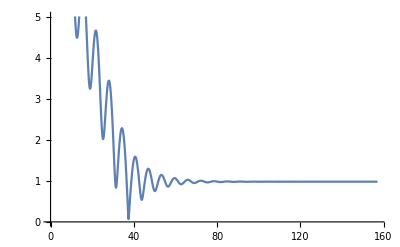

```mathematica
alpha = 0.2
Fr[R_,phi_]:=Sin[phi]-alpha
Fphi[R_,phi_]:=Cos[phi]/R-1
s=NDSolve[{R'[theta]==Fr[R[theta],phi[theta]], phi'[theta]==Fphi[R[theta],phi[theta]],{R[0]==7,phi[0]==Pi}},{R,phi},{theta, 0, 50Pi}]
Plot[Evaluate[R[theta]]/.s, {theta,0,50Pi}]
```

0.9

{{R→InterpolatingFunction[{{0., 157.08}}, <>],phi→InterpolatingFunction[{{0., 157.08}}, <>]}}

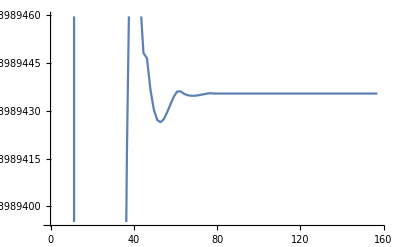

```mathematica
alpha = 0.9
Fr[R_,phi_]:=Sin[phi]-alpha
Fphi[R_,phi_]:=Cos[phi]/R-1
s=NDSolve[{R'[theta]==Fr[R[theta],phi[theta]], phi'[theta]==Fphi[R[theta],phi[theta]],{R[0]==7,phi[0]==Pi}},{R,phi},{theta, 0, 50Pi}]
Plot[Evaluate[R[theta]]/.s, {theta,0,50Pi}]
```

1

{{R→InterpolatingFunction[{{0., 157.08}}, <>],phi→InterpolatingFunction[{{0., 157.08}}, <>]}}

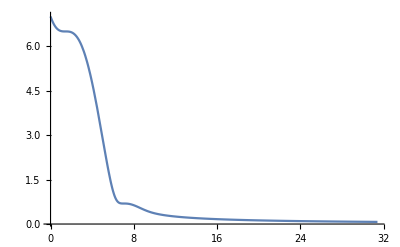

```mathematica
alpha = 1
Fr[R_,phi_]:=Sin[phi]-alpha
Fphi[R_,phi_]:=Cos[phi]/R-1
s=NDSolve[{R'[theta]==Fr[R[theta],phi[theta]], phi'[theta]==Fphi[R[theta],phi[theta]],{R[0]==7,phi[0]==Pi}},{R,phi},{theta, 0, 50Pi}]
Plot[Evaluate[R[theta]]/.s, {theta,0,10Pi},PlotRange->All]
```

1.5

{{R→InterpolatingFunction[{{0., 157.08}}, <>],phi→InterpolatingFunction[{{0., 157.08}}, <>]}}

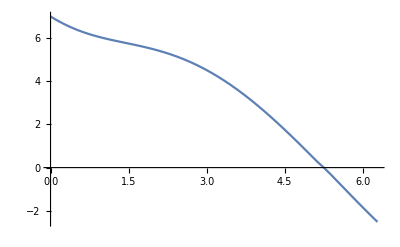

NDSolve::overdet: There are fewer dependent variables, {theta[t]}, than equations, so the system is overdetermined.

```mathematica
alpha = 1.5
Fr[R_,phi_]:=Sin[phi]-alpha
Fphi[R_,phi_]:=Cos[phi]/R-1
s=NDSolve[{R'[theta]==Fr[R[theta],phi[theta]], phi'[theta]==Fphi[R[theta],phi[theta]],{R[0]==7,phi[0]==Pi}},{R,phi},{theta, 0, 50Pi}]
Plot[Evaluate[R[theta]]/.s, {theta,0,2Pi},PlotRange->All]
```